```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
β[0,δ,1,0,5]//MatrixForm
```

(ⅈ δ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | ⅈ δ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | ⅈ δ | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | ⅈ δ | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | ⅈ δ | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | ⅈ δ | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | ⅈ δ | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | -1 | ⅈ δ | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | ⅈ δ | -1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | ⅈ δ)

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
T1[1,12]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[0,0.0001,0.5,0,9]
```

1.6×10^-6

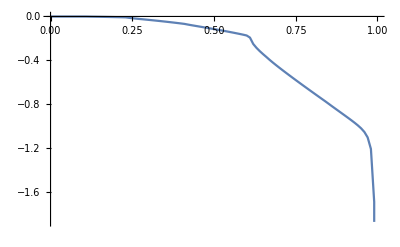
{1552.29,-Graphics-}

```mathematica
Monitor[Timing[ListLinePlot[Table[{ω,Im[SL[ω,0.001,1,0,15][[1,1]]]},{ω,Range[0,1,0.01]}]]],ω]
```

```mathematica
list[m_,num_]:=RandomSample[Transpose[Join[Table[0,100-num],Table[RandomInteger[{1,2*m}],num]]]]
```

```mathematica
dist[m_,num_]:=dist[m,num]=Table[Transpose[Join[{Range[1,100,1]},{list[m,num]}]],4000]
```

```mathematica
list[17,6*17]
```

{19,34,7,13,34,14,31,26,21,3,30,7,33,26,27,14,30,2,20,11,23,25,19,13,9,30,13,24,10,1,33,20,19,32,33,12,10,26,29,15,31,29,9,3,33,25,17,33,31,18,3,11,8,5,18,30,14,24,20,2,28,34,17,17,21,12,13,17,7,24,25,14,1,26,23,27,16,29,27,3,7,29,26,10,13,22,31,13,24,15,18,23,3,12,27,32,21,15,34,22,21,29}

```mathematica
CAvg[ω_,δ_,t_,ϵ_,ϵ1_,m_,conc_,number_]:= Module[{Tin=T1[1,m],T=ρ[1,m]},
sl1= Module[{J=SL[ω,δ,1,0,m]},Do[J=Inverse[IdentityMatrix[2m]-Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n= dist[m,conc][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].ConjugateTranspose[Tin].J.Tin].Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n= dist[m,conc][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]],{loc1,1,100}];J=J];Il1:=Inverse[IdentityMatrix[2m]-sl1.T.SR[ω,δ,1,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,1,0,m].T.sl1.T].SR[ω,δ,1,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,1,0,m],tr[ω,δ,1,0,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]]
```

```mathematica
Clear[ca]
```

```mathematica
ca[dim_,conc_]:=ca[dim,conc]=Monitor[Table[CAvg[1,0.001,1,0,0.5,dim,conc,number],{number,3000}],number]
```

```mathematica
Range[3,40,4]
```

{3,7,11,15,19,23,27,31,35,39}

```mathematica
Monitor[Table[ca[m,6*m],{m,Range[3,19,4]}],m]
```

{{0.84392,0.717753,0.780585,0.913551,0.671711,0.832235,0.97008,0.879652,0.502788,0.889612,2980,0.864334,0.981965,0.862083,0.732625,0.750576,0.899346,0.734445,0.932984,0.721816,0.706115},3,{1}}
 |  |  |  |

```mathematica
ca[15,6*15]
```

```mathematica
Table[{x,Abs[Mean[ca[7,30][[1;;x]]]-Mean[ca[7,30][[1;;x+1]]]]},{x,5,950,50}]
```

```mathematica
ca[7,30][[1;;2]]
```

{1.99158,2.66867}

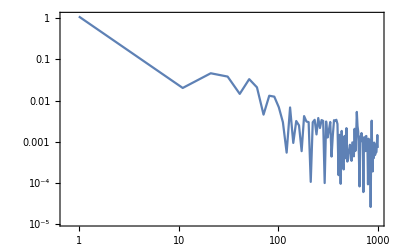

```mathematica
ListLogLogPlot[Table[{x,Abs[Mean[ca[15,6*15][[1;;x]]]-Mean[ca[15,6*15][[1;;x+1]]]]},{x,1,1000,10}],Joined->True,PlotRange->All,Frame->True]
```

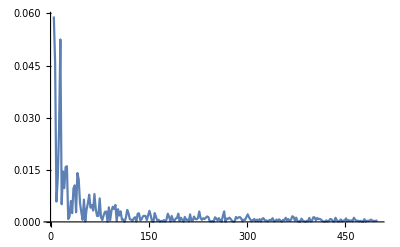

```mathematica
ListPlot[%70,Joined->True,PlotRange->All]
```